```mathematica
listk10 ={{8,0.0645938208366452},{10,0.043548290335308},{12,0.0310111443096394},{14,0.0234412481682771},{16,0.0181333473707647}}
```

{{8,0.0645938},{10,0.0435483},{12,0.0310111},{14,0.0234412},{16,0.0181333}}

```mathematica
listk9 ={{8,0.111856541046938},{10,0.0789968556225624},{12,0.0636404578639337},{14,0.040492580001731},{16,0.0341861057119987}}
```

{{8,0.111857},{10,0.0789969},{12,0.0636405},{14,0.0404926},{16,0.0341861}}

```mathematica
listk8 = {{8,0.115024589707177},{10,0.0777331235396553},{12,0.0603175911763468},{14,0.0412715327443922},{16,0.0369050163149535}}
```

{{8,0.115025},{10,0.0777331},{12,0.0603176},{14,0.0412715},{16,0.036905}}

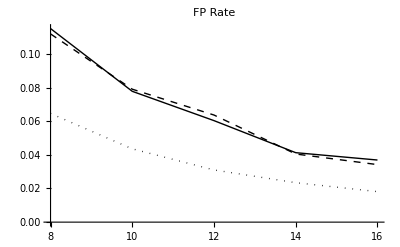

```mathematica
fp =ListPlot[{listk8, listk9,listk10},Joined->True,PlotStyle->{Black,{Black,Dashed},{Black,Dotted}},PlotLabel->"FP Rate",BaseStyle->{FontSize->16}]
```

```mathematica
list10bad={{8,842568},{10,473287},{12,307053},{14,204918},{16,143991}}
```

{{8,842568},{10,473287},{12,307053},{14,204918},{16,143991}}

```mathematica
{{8,842568},{10,473287},{12,307053},{14,204918},{16,143991}}
```

{{8,842568},{10,473287},{12,307053},{14,204918},{16,143991}}

```mathematica
list9bad={{8,1554351},{10,956315},{12,708804},{14,402361},{16,317874}}
```

{{8,1554351},{10,956315},{12,708804},{14,402361},{16,317874}}

```mathematica
list8bad={{8,1661655},{10,973830},{12,687746},{14,411000},{16,362480}}
```

{{8,1661655},{10,973830},{12,687746},{14,411000},{16,362480}}

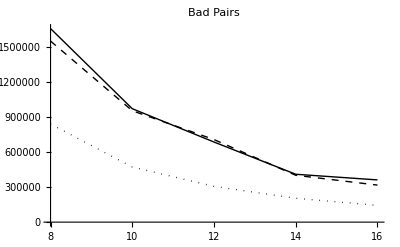

```mathematica
bd = ListPlot[{list8bad, list9bad,list10bad},Joined->True,PlotStyle->{Black,{Black,Dashed},{Black,Dotted}},PlotLabel->"Bad Pairs",BaseStyle->{FontSize->16}]
```

```mathematica
list10good={{8,13044096},{10,10868096},{12,9901376},{14,8741770},{16,7940674}}
```

{{8,13044096},{10,10868096},{12,9901376},{14,8741770},{16,7940674}}

```mathematica
list9good={{8,13895933},{10,12105735},{12,11137632},{14,9936660},{16,9298339}}
```

{{8,13895933},{10,12105735},{12,11137632},{14,9936660},{16,9298339}}

```mathematica
list8good={{8,14446085},{10,12527864},{12,11402080},{14,9958438},{16,9821971}}
```

{{8,14446085},{10,12527864},{12,11402080},{14,9958438},{16,9821971}}

```mathematica
lg =LineLegend[{Black,{Black,Dashed},{Black,Dotted}},{"k=8", "k=9","k=10"}]
```

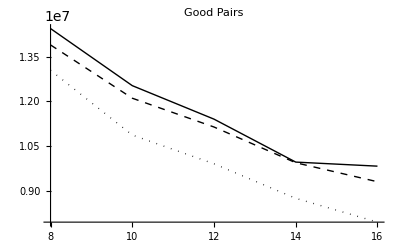

```mathematica
gd = ListPlot[{list8good, list9good,list10good},Joined->True,PlotStyle->{Black,{Black,Dashed},{Black,Dotted}},PlotLabel->"Good Pairs",BaseStyle->{FontSize->16}]
```

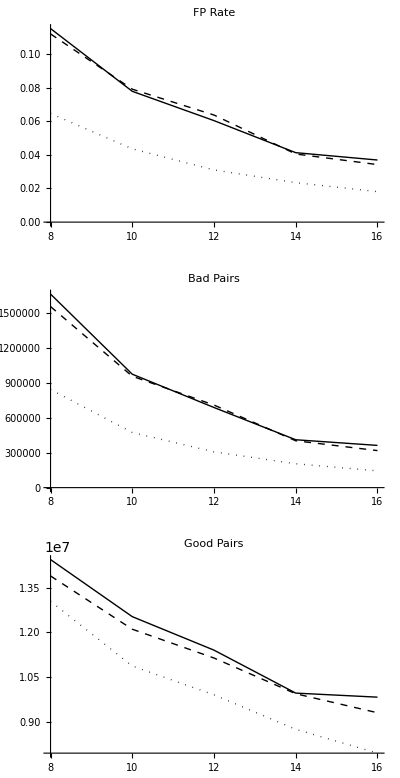

```mathematica
Legended[GraphicsGrid[{{fp},{bd},{gd}},ImageSize-> Scaled[.5]],lg]
```

```mathematica
Export["edgridl.eps",Legended[GraphicsGrid[{{fp},{bd},{gd}},ImageSize-> Scaled[.5]],lg]]
```

edgridl.eps

edgrid.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["edgrid.eps"]]]
```